# A Generalised Maxwell Stress Tensor for Semi-Analytic Force and Torque Between Permanent Magnets, Coils, and Soft Iron

Matthew Forbes, Will Robertson, Anthony Zander, James Vidler

The University of Adelaide

Johan Paulides

Advanced Electromagnetics Group

Supplemental material (https://doi.org/). A related online repository can be found at: https://github.com/AUMAG/mag-gmst-force. This document uses the Generalised Maxwell Stress Tensor (GMST) and MST to calculate 3D force and torque on a region using elemental magnetic field solutions.  Provided is the package MagCylField (Section 0.3) that can be used to calculate the magnetic field from cylindrical arc magnets and coils. A single case study is (currently) shown where the force and torque is calculated between diametrically magnetised arcs using a cuboid closed-surface mesh (Section 1). The results are compared to an FEA model herein and  in the Appendix of the  published article.

If you are reading this in PDF format, note the code is truncated. There is a Mathematica notebook ‘.nb’ file that contains full functionality and a package ‘.wl’ file that contains the nomenclature and magnetic field equations. If you do not have a paid/trial version of Mathematica, this notebook can be opened in a free player (e.g Wolfram Player https://www.wolfram.com/player/) in order to view/copy the tensors/equations. There are also built-in or addon functions that can convert the equations to MATLAB, LATEX, Python, etc...

The code below is not written to optimise computational speed. This serves as a visualisation with example usage.

The field points (and sometimes source points) need to be rounded to $MachineEpsilon to ensure the memoization for special cases correctly executes. This otherwise leads to undefined or infinite results.

The magnetic field functions will return values in Cylindrical coordinates unless ρ=0.

It is useful to operate in both Cylindrical and Cartesian coordinates for the calculations and visualisations (and to check results). There is no error handling if a mesh field point is along the axis as the point in Cylindrical coordinates is undefined. It is suggested to avoid ρ=0 (x=0 && y=0), even though the field functions will accept this and return a correct value (in Cartesian coordinates).

Mathematica uses complex numbers for the evaluation of ArcTan, ArcTanh,... and as such these return real numbers of the form a+0.ⅈ when converted to a numerical value using ‘//N’ (this is useful for not keeping all values symbolic). We use ‘//Chop’ to remove numerical 0.ⅈ terms.

## 0.1 Citations for this work

M. Forbes, W.S.P Robertson, A.C. Zander, J. Vidler, J.J.H. Paulides, "A Generalised Maxwell Stress Tensor for Semi-Analytic Force and Torque Between Permanent Magnets, Coils, and Soft Iron"

@Article {Forbes2025,
        author = {Forbes, M. and Robertson, W.S.P. and Zander, A.C. and Vidler, J. and Paulides, J.J.H},
        journal = {Preprint},
        title = {A Generalised Maxwell Stress Tensor for Semi-Analytic Force and Torque Between Permanent Magnets, Coils, and Soft Iron},
        doi = {},
        publisher = {},
 }

M. Forbes, W.S.P Robertson, A.C. Zander, J.J.H. Paulides, "The Magnetic Field from Cylindrical Arc Coils and Magnets: A Compendium with New Analytic Solutions for Radial Magnetisation and Azimuthal Current"

@Article {Forbes2024,
        author = {Forbes, M. and Robertson, W.S.P. and Zander, A.C. and Paulides, J.J.H},
        journal = {Advanced Physics Research},
        title = {The Magnetic Field from Cylindrical Arc Coils and Magnets: A Compendium with New Analytic Solutions for Radial Magnetisation and Azimuthal Current},
        doi = {10.1002/apxr.202300136},
        publisher = {Wiley},
        number = {7},
        pages = {2300136},
        volume = {3}
 }

## 0.2 Tensors

FGMST and TGMST are the Generalised Maxwell Stress Tensors (GMST)  for  force and torque. FMST and TMST are the Maxwell Stress Tensors (MST)  for force and torque.

```mathematica
FMST[Bx_,By_,Bz_] := u0^-1{{1/2(Bx^2-By^2-Bz^2),Bx By,Bx Bz},{Bx By,1/2(-Bx^2+By^2-Bz^2),By Bz},{Bx Bz,By Bz,1/2(-Bx^2-By^2+Bz^2)}};
TMST[x_,y_,z_,Bx_,By_,Bz_] := u0^-1{{-z Bx By+y Bx Bz,-z By^2+y By Bz+1/2 z (Bx^2+By^2+Bz^2),-z By Bz+y Bz^2-1/2 y (Bx^2+By^2+Bz^2)},{z Bx^2-x Bx Bz-1/2 z (Bx^2+By^2+Bz^2),z Bx By-x By Bz,z Bx Bz-x Bz^2+1/2 x (Bx^2+By^2+Bz^2)},{-y Bx^2+x Bx By+1/2 y (Bx^2+By^2+Bz^2),-y Bx By+x By^2-1/2 x (Bx^2+By^2+Bz^2),-y Bx Bz+x By Bz}};
FGMST[BEx_,BEy_,BEz_,BIx_,BIy_,BIz_] := u0^-1{{BEx BIx-BEy BIy-BEz BIz,BEy BIx+BEx BIy,BEz BIx+BEx BIz},{BEy BIx+BEx BIy,-BEx BIx+BEy BIy-BEz BIz,BEz BIy+BEy BIz},{BEz BIx+BEx BIz,BEz BIy+BEy BIz,-BEx BIx-BEy BIy+BEz BIz}};
TGMST[x_,y_,z_,BEx_,BEy_,BEz_,BIx_,BIy_,BIz_] := u0^-1{{-z(BEx BIy+BEy BIx)+y(BEx BIz+BEz BIx),y(BEy BIz+BEz BIy)+z(BEx BIx-BEy BIy+BEz BIz),-z(BEy BIz+BEz BIy)-y(BEx BIx+BEy BIy-BEz BIz)},{-x(BEx BIz+BEz BIx)+z(BEx BIx-BEy BIy-BEz BIz),z(BEx BIy+BEy BIx)-x(BEy BIz+BEz BIy),z(BEx BIz+BEz BIx)+x(BEx BIx+BEy BIy-BEz BIz)},{x(BEx BIy+BEy BIx)+y(-BEx BIx+BEy BIy+BEz BIz),-y(BEx BIy+BEy BIx)-x(BEx BIx-BEy BIy+BEz BIz),x(BEy BIz+BEz BIy)-y(BEx BIz+BEz BIx)}};

u0 FGMST[Subscript[B, 𝓍]^("E"),Subscript[B, 𝓎]^("E"),Subscript[B, 𝓏]^("E"),Subscript[B, 𝓍]^("I"),Subscript[B, 𝓎]^("I"),Subscript[B, 𝓏]^("I")]//MatrixForm
u0 TGMST[𝓍,𝓎,𝓏,Subscript[B, 𝓍]^("E"),Subscript[B, 𝓎]^("E"),Subscript[B, 𝓏]^("E"),Subscript[B, 𝓍]^("I"),Subscript[B, 𝓎]^("I"),Subscript[B, 𝓏]^("I")]//MatrixForm
```

(B_𝓍^E B_𝓍^I-B_𝓎^E B_𝓎^I-B_𝓏^E B_𝓏^I | B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I | B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I
B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I | -B_𝓍^E B_𝓍^I+B_𝓎^E B_𝓎^I-B_𝓏^E B_𝓏^I | B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I
B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I | B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I | -B_𝓍^E B_𝓍^I-B_𝓎^E B_𝓎^I+B_𝓏^E B_𝓏^I)

(-𝓏 (B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I)+𝓎 (B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I) | 𝓎 (B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I)+𝓏 (B_𝓍^E B_𝓍^I-B_𝓎^E B_𝓎^I+B_𝓏^E B_𝓏^I) | -𝓏 (B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I)-𝓎 (B_𝓍^E B_𝓍^I+B_𝓎^E B_𝓎^I-B_𝓏^E B_𝓏^I)
-𝓍 (B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I)+𝓏 (B_𝓍^E B_𝓍^I-B_𝓎^E B_𝓎^I-B_𝓏^E B_𝓏^I) | 𝓏 (B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I)-𝓍 (B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I) | 𝓏 (B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I)+𝓍 (B_𝓍^E B_𝓍^I+B_𝓎^E B_𝓎^I-B_𝓏^E B_𝓏^I)
𝓍 (B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I)+𝓎 (-B_𝓍^E B_𝓍^I+B_𝓎^E B_𝓎^I+B_𝓏^E B_𝓏^I) | -𝓎 (B_𝓍^I B_𝓎^E+B_𝓍^E B_𝓎^I)-𝓍 (B_𝓍^E B_𝓍^I-B_𝓎^E B_𝓎^I+B_𝓏^E B_𝓏^I) | -𝓎 (B_𝓍^I B_𝓏^E+B_𝓍^E B_𝓏^I)+𝓍 (B_𝓎^I B_𝓏^E+B_𝓎^E B_𝓏^I))

## 0.3 Import Cylindrical Magnetic Field Equations

The MagCylField package was created for this article using the work from our previous article https://doi.org/10.1002/apxr.202300136, with the supplemental material https://github.com/AUMAG/mag-cyl-field.

This notebook file and package assume the user has Mathematica 12.3 or later. If this is not the case, you will need to include the (commented out) Carlson package in both files https://github.com/tpfto/Carlson/tree/v1.1 oi.

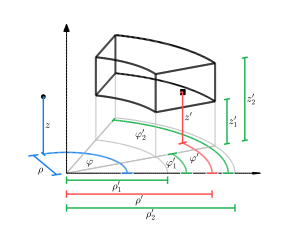

```mathematica
SetDirectory[NotebookDirectory[]];
<< MagCylField` (* Needs["Carlson`"] *)
(* << Carlson`  Used for some backwards compatibility with a special case of EllipticF[ϕ,1], and not required in 12.3 or later: https://reference.wolfram.com/language/ref/CarlsonRC.html *)
```

Brief README.

```mathematica
(*  CylB𝒹: Diametric magnetisation 
	CylBρ: Radial magnetisation 
	CylBφ: Azimuthal magnetisation, 
	CylB𝓏: Axial magnetisation, 
	CylBℐ𝒻: Azmimuthal current filament, 
	CylB𝒦𝒹: Azmimuthal current disc,
	CylB𝒦𝓈: Azmimuthal current shell, 
	CylB𝒥𝓋: Azmimuthal current volume  *)
CylB𝒹::usage
```

Diametric magnetisation
 CylB𝒹[M,φ☆,{ρ_1',ρ_2'},ρ,{φ_1',φ_2'},φ,{z_1',z_2'},z] with: M magnetisation magnitude (A/m), φ☆ magnetision direction (rad), r' source limits (m,rad,m), r field point (m,rad,m).
 Returns the magnetic field in cylindrical coordinates for ρ≠0 and Cartesian coordinates for ρ=0. 
 Points on the magnet surface are (potentially) undefined.

## 0.4 Constants

```mathematica
u0 = 4π*10^-7; (*N/A^2*)
```

## 0.5 Plot functions

Plots the arc sectors, and mesh frame with normal vectors and centroids.

```mathematica
MagOpts[col_]:={Mesh->None,PlotPoints->{2,100},BoundaryStyle->Off,MeshShading-> Off,PlotStyle-> {col,Opacity[1]}};
HollowCylinderSector[r1_,r2_,θ1_,θ2_,z1_,z2_,col_]:={Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{z,z1,z2},{θ,θ1, θ2},Evaluate[MagOpts[col]]],{r,{r1,r2}}],Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{r,r1,r2},{θ,θ1, θ2},Evaluate[MagOpts[col]]],{z,{z1,z2}}],Table[ParametricPlot3D[{r Cos[θ],r Sin[θ],z},{r,r1,r2},{z,z1,z2},Evaluate[MagOpts[col]]],{θ,{θ1, θ2}}]}
PlotMesh[meshData_] := 
	Module[{size,i,framePlot,centroidPlot,normalPlot,normals,points,scale,radiusPlot},
		size = Dimensions[meshData][[1]];
		framePlot= ConstantArray[0,size];
		centroidPlot= ConstantArray[0,size];
		normalPlot= ConstantArray[0,size];
		radiusPlot= ConstantArray[0,size];
		scale=0.001;
		For[i=1,i<size+1,i++,
			normals =Cyl2CartField[meshData[[i,3,;;]],meshData[[i,5,;;]]];
			points = meshData[[i,3,;;]];
		    framePlot[[i]] =MeshFrame[meshData[[i]]] ;
			centroidPlot[[i]] = MeshPoints[meshData[[i]]];
			normalPlot[[i]]=Graphics3D[{Black,Opacity[1],Arrowheads[Small],Table[{Arrow[{{points[[j,1]],points[[j,2]],points[[j,3]]},{points[[j,1]],points[[j,2]],points[[j,3]]}+scale{ normals[[j,1]],normals[[j,2]],normals[[j,3]]}}]},{j,1,Dimensions[normals][[1]]}]}];
		];
	Show[framePlot[[#]]&/@Range[1,size],centroidPlot[[#]]&/@Range[1,size],normalPlot[[#]]&/@Range[1,size]]
	]
```

## 0.6 Mesh functions

Generates six planar surface meshes to form a closed surface around one collection of magnetic sources.

This may not be an optimal mesh geometry, but is intentionally contrasting to the magnet geometry.

```mathematica
MeshFaces[ptx_,pty_] :=Flatten[Table[{j*ptx+i,j*ptx+i+1,(j-1)*ptx+i+1,(j-1)*ptx+i},{i,1,ptx-1},{j,1,pty-1}],1];
MeshCentroids[coordinates_,faces_] := Table[RegionCentroid[Polygon[coordinates[[faces[[i]]]]]],{i,1,Dimensions[faces,1][[1]]}];
MeshAreas[coordinates_,faces_] := Table[RegionMeasure[Polygon[coordinates[[faces[[i]]]]]],{i,1,Dimensions[faces,1][[1]]}];
MeshFrame[sdata_] := Graphics3D[{EdgeForm[Black],FaceForm[ ],Table[Polygon[sdata[[1]][[sdata[[2]][[i]]]]],{i,1,Dimensions[sdata[[2]],1][[1]]}]},Boxed->False]
MeshPoints[sdata_] := ListPointPlot3D[sdata[[3]],Axes->False,Boxed->False,PlotStyle-> {Black,PointSize[Small]}]
CuboidMesh[ptx_,pty_,ptz_,x1_,x2_,y1_,y2_,z1_,z2_]:= 
Module[{mesh1,mesh2,mesh3,mesh4,mesh5,mesh6},
	mesh1= CartSurface["X+",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	mesh2 = CartSurface["X-",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	mesh3 = CartSurface["Y+",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	mesh4 = CartSurface["Y-",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	mesh5 = CartSurface["Z+",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	mesh6 = CartSurface["Z-",ptx,pty,ptz,x1,x2,y1,y2,z1,z2];
	{mesh1,mesh2,mesh3,mesh4,mesh5,mesh6}
]
CartSurface[desc_,ptx_,pty_,ptz_,x1_,x2_,y1_,y2_,z1_,z2_] := 
	Module[{n,x,y,z,coordinatesCart,faces,centroidsCart,meshArea,normalsCart,coordinatesCyl,centroidsCyl,noElements,normalsCyl},
	Which[desc == "Z+",
			n=1;z=z2;
			coordinatesCart=Flatten[Table[{x,y,z},{x,x1,x2,(x2-x1)/(ptx-1)},{y,y1,y2,(y2-y1)/(pty-1)}],1]//N;
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[N[x],y],z},{x,x1,x2,(x2-x1)/(ptx-1)},{y,y1,y2,(y2-y1)/(pty-1)}],1]//N;
			faces=MeshFaces[pty,ptx];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			normalsCart =Table[{0,0,n},{i,1,noElements}];
			normalsCyl=normalsCart,
		desc == "Z-",
			n=-1;z=z1;
			 coordinatesCart=Flatten[Table[{x,y,z},{x,x1,x2,(x2-x1)/(ptx-1)},{y,y1,y2,(y2-y1)/(pty-1)}],1]//N;
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[N[x],y],z},{x,x1,x2,(x2-x1)/(ptx-1)},{y,y1,y2,(y2-y1)/(pty-1)}],1]//N;
			faces=MeshFaces[pty,ptx];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			normalsCart =Table[{0,0,n},{i,1,noElements}];
			normalsCyl=normalsCart,
		desc == "Y+",
			n=0;y=y2;
			coordinatesCart=Flatten[Table[{x,y,z},{x,x1,x2,(x2-x1)/(ptx-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[x,y],z},{x,x1,x2,(x2-x1)/(ptx-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			faces=MeshFaces[ptz,ptx];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			x = centroidsCart[[;;,1]];
			normalsCart =Table[{0,1 ,0},{i,1,noElements}];
			normalsCyl =Table[{Sin[ArcTan[x[[i]],y]+n],Cos[ArcTan[x[[i]],y]+n] ,0},{i,1,noElements}],
		desc == "Y-",
			n=π;y=y1;
			coordinatesCart=Flatten[Table[{x,y,z},{x,x1,x2,(x2-x1)/(ptx-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[x,y],z},{x,x1,x2,(x2-x1)/(ptx-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			faces=MeshFaces[ptz,ptx];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			x = centroidsCart[[;;,1]];
			normalsCart =Table[{0,-1 ,0},{i,1,noElements}];
			normalsCyl =Table[{Sin[ArcTan[x[[i]],y]+n],Cos[ArcTan[x[[i]],y]+n] ,0},{i,1,noElements}],
		desc == "X+",
			n=0;x=x2;
			coordinatesCart=Flatten[Table[{x,y,z},{y,y1,y2,(y2-y1)/(pty-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[x,y],z},{y,y1,y2,(y2-y1)/(pty-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			faces=MeshFaces[ptz,pty];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			y = centroidsCart[[;;,2]];
			normalsCyl =Table[{Cos[ArcTan[x,y[[i]]]+n],-Sin[ArcTan[x,y[[i]]]+n] ,0},{i,1,noElements}];
			normalsCart =Table[{1,0 ,0},{i,1,noElements}],
		desc == "X-",
			n=π;x=x1;
			coordinatesCart=Flatten[Table[{x,y,z},{y,y1,y2,(y2-y1)/(pty-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;	
			coordinatesCyl=Flatten[Table[{√(x^2+y^2),ArcTan[x,y],z},{y,y1,y2,(y2-y1)/(pty-1)},{z,z1,z2,(z2-z1)/(ptz-1)}],1]//N;
			faces=MeshFaces[ptz,pty];
			noElements = Dimensions[faces,1][[1]];
			centroidsCart = MeshCentroids[coordinatesCart,faces];
			y = centroidsCart[[;;,2]];
			normalsCyl =Table[{Cos[ArcTan[x,y[[i]]]+n],-Sin[ArcTan[x,y[[i]]]+n] ,0},{i,1,noElements}];
			normalsCart =Table[{-1,0 ,0},{i,1,noElements}]
	];
	centroidsCyl = Cart2Cyl[centroidsCart];
	meshArea = MeshAreas[coordinatesCart,faces];
	{coordinatesCart,faces,centroidsCart,meshArea,normalsCyl,coordinatesCyl,centroidsCyl,noElements,normalsCart}
]
```

## 0.7 Transforms

```mathematica
Cart2Cyl[pts_] :=CoordinateTransform["Cartesian"->"Cylindrical",pts] 
Cyl2CartField[pts_,vals_] := 
	Module[{valX,valY,valZ},
		valX = vals[[;;,1]] Cos[ArcTan[pts[[;;,1]],pts[[;;,2]]]]-vals[[;;,2]] Sin[ArcTan[pts[[;;,1]],pts[[;;,2]]]]//Chop;
		valY = vals[[;;,1]]Sin[ArcTan[pts[[;;,1]],pts[[;;,2]]]]+vals[[;;,2]] Cos[ArcTan[pts[[;;,1]],pts[[;;,2]]]]//Chop;
		valZ= vals[[;;,3]];
		Table[{valX[[i]],valY[[i]],valZ[[i]]},{i,1,Length@valX}]
	]
```

## 0.8 Figure and result table

```mathematica
Cart2Cyl[pts_] :=CoordinateTransform["Cartesian"->"Cylindrical",pts] 
DiametricExample[order_,noMags_,meshTol_,x☆_,y☆_,z☆_,φ☆_,ME_,ρʹ_,zʹ_,MI_,ρ_,φ_,z_] := 
	Module[{ptx,pty,ptz,φʹ,IntegralMesh,surfaceAreas,surfaceNormals,fieldPoints,fieldPointsc,meshElements,BI,BE,MagRing,BEc,BIc,ForceMST,TorqueMST,ForceGMST,TorqueGMST,ForceFEA,TorqueFEA,fig,tab,tmp,n,MagArc,IntegralMeshPlot,heading},
		ptx = Round[(x☆[[2]]- x☆[[1]])/meshTol]; (* Points to create square mesh (approximately 1:1 ratio) *)
		If[EvenQ[ptx[[#]]],ptx[[#]]++]& /@ {1,2}; (* Simple avoidance of ArcTan[0,0] *)
		pty = Round[(y☆[[2]]- y☆[[1]])/meshTol];
		If[EvenQ[pty[[#]]],pty[[#]]++]& /@ {1,2};
		ptz = Round[(z☆[[2]]- z☆[[1]])/meshTol];
		
		(* Mesh around one collection (second is coarse plot mesh) *)
		IntegralMesh = CuboidMesh[ptx[[2]],pty[[2]],ptz[[2]],x☆[[1]],x☆[[2]], y☆[[1]], y☆[[2]],z☆[[1]],z☆[[2]]];
		IntegralMeshPlot = CuboidMesh[ptx[[1]],pty[[1]],ptz[[1]],x☆[[1]],x☆[[2]], y☆[[1]], y☆[[2]],z☆[[1]],z☆[[2]]];
		(* Unpack data from the integration closed surface mesh *)
		surfaceAreas = Flatten[IntegralMesh[[;;,4]],1];
		surfaceNormals = Flatten[IntegralMesh[[;;,9]],1];
		fieldPoints = Flatten[IntegralMesh[[;;,7]],1];
		fieldPointsc = Flatten[IntegralMesh[[;;,3]],1];
		meshElements = Total[Flatten[IntegralMesh[[;;,8]],1]];
		(* Internal magnetic field and plot PM*)
		BI = Table[CylB𝒹[MI,φ☆[[1]],Round[ρ,2$MachineEpsilon],Round[fieldPoints[[i,1]],2$MachineEpsilon],Round[φ,$MachineEpsilon],Round[fieldPoints[[i,2]],$MachineEpsilon],Round[z,$MachineEpsilon],Round[fieldPoints[[i,3]],$MachineEpsilon]],{i,1,Length@fieldPoints}];
		MagArc = Show[HollowCylinderSector[ρ[[1]],ρ[[2]],φ[[1]],φ[[2]],z[[1]],z[[2]],RGBColor[Rational[51, 256], Rational[5, 8], Rational[11, 64]]]];
		(* External magnetic field and plot PMs *)
		BE = ConstantArray[0,noMags];
		MagRing = ConstantArray[0,noMags];
		For[n=1, n<noMags+1, n++,
			φʹ = {n π/2+π/32,(n+1)π/2-π/32};
			MagRing[[n]] = Show[HollowCylinderSector[ρʹ[[1]],ρʹ[[2]],φʹ[[1]],φʹ[[2]],zʹ[[1]],zʹ[[2]],RGBColor[Rational[227, 256], Rational[13, 128], Rational[7, 64]]]];
			BE[[n]] = Table[CylB𝒹[ME,φ☆[[n+1]],ρʹ,Round[fieldPoints[[i,1]],$MachineEpsilon],φʹ,Round[fieldPoints[[i,2]],$MachineEpsilon],zʹ,Round[fieldPoints[[i,3]],$MachineEpsilon]],{i,1,Length@fieldPoints}];
		];
		(* Sum external contributions *)	
		BE = Total[BE,1];
		(* FEA Results are converged to the number of displayed significant figures. *)
		ForceFEA = {0.371,0.123,1.013}; (* N *)
		TorqueFEA = {-0.698,-1.002,1.287}; (* mNm *)
		If[order=="Inverse",tmp=BI;BI=BE;BE=tmp;ForceFEA=-ForceFEA;TorqueFEA=-TorqueFEA;];
		
		(* Convert to Cartesian *)
		BEc = Cyl2CartField[fieldPointsc, BE];
		BIc = Cyl2CartField[fieldPointsc, BI];
		
		ForceMST = Total[Table[FMST[BEc[[i,1]]+BIc[[i,1]],BEc[[i,2]]+BIc[[i,2]],BEc[[i,3]]+BIc[[i,3]]].surfaceNormals[[i]]*surfaceAreas[[i]],{i,1,Length@surfaceAreas}],1];
		TorqueMST = Total[Table[TMST[fieldPointsc[[i,1]],fieldPointsc[[i,2]],fieldPointsc[[i,3]],BEc[[i,1]]+BIc[[i,1]],BEc[[i,2]]+BIc[[i,2]],BEc[[i,3]]+BIc[[i,3]]].surfaceNormals[[i]]*surfaceAreas[[i]],{i,1,Length@surfaceAreas}],1];
		ForceGMST = Total[Table[FGMST[BEc[[i,1]],BEc[[i,2]],BEc[[i,3]],BIc[[i,1]],BIc[[i,2]],BIc[[i,3]]].surfaceNormals[[i]]*surfaceAreas[[i]],{i,1,Length@surfaceAreas}],1];
		TorqueGMST = Total[Table[TGMST[fieldPointsc[[i,1]],fieldPointsc[[i,2]],fieldPointsc[[i,3]],BEc[[i,1]],BEc[[i,2]],BEc[[i,3]],BIc[[i,1]],BIc[[i,2]],BIc[[i,3]]].surfaceNormals[[i]]*surfaceAreas[[i]],{i,1,Length@surfaceAreas}],1];
		
		(* Create illustration and results table *)
		fig = Show[MagRing[[#]]&/@Range[1,noMags],MagArc,PlotMesh[IntegralMeshPlot],Boxed->True,Axes->True,AxesLabel->{"x","y","z"},ImageSize->Large,ViewProjection->"Orthographic",ViewPoint->{-1.55,-2.30,1.93},ViewVertical->{-0.0036,-0.015,1}];
		heading = {"Elements","F_𝓍, N","F_𝓎, N","F_𝓏, N","T_𝓍, mN·m","T_𝓎, mN·m","T_𝓏, mN·m"} ;  
		tab = TableForm[{Join[{meshElements},Round[ForceMST,0.001],Round[TorqueMST*1000,0.001]],Join[{meshElements},Round[ForceGMST,0.001],Round[TorqueGMST*1000,0.001]],Join[{"N/A"},ForceFEA,TorqueFEA]}, TableHeadings -> {{"MST", "GMST", "FEA"}, heading}];
		CellPrint[{ExpressionCell[tab, "Output"],fig}]
	]
```

## 1.0 Case study 1: Diametrically magnetised PMs

### 1.1 Geometry

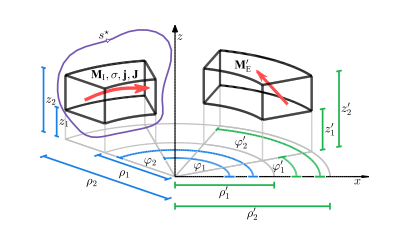

PM details.

```mathematica
ME = 955*10^3; (*A/m*)
MI = 800*10^3; (*A/m*)
ρʹ = {5/1000,10/1000};  zʹ = {0/1000,5/1000}; (*ME definite integral limits*) 
ρ = {5/1000,10/1000}; φ = {π/32,π/4}; z = {6/1000,11/1000};  (*MI definite integral limits*) 
meshTol={2/1000,1/2000}; (* Scaling for mesh spacing {figure, calculation} *)
noMags=3; (* Number of magnets in lower ring -- FEA result only valid for 3 *)
φ☆=(2π)/(noMags+1)(#-1/2)&/@ Range[1,noMags+1];(* Diametric magnetisation directions *)
```

### 1.2 Primary result

Mesh details.

```mathematica
x☆ = {3/1000,21/2000}; y☆= {0/1000,15/2000}; z☆ = {11/2000,23/2000};  (*GMST definite integral limits*)
```

Results table and visualisation plot.

Accuracy and computational cost increases with increasing meshTol.

```mathematica
DiametricExample["Standard",noMags,meshTol,x☆,y☆,z☆,φ☆,ME,ρʹ,zʹ,MI,ρ,φ,z]
```

| Elements | F_𝓍, N | F_𝓎, N | F_𝓏, N | T_𝓍, mN·m | T_𝓎, mN·m | T_𝓏, mN·m
MST | 1008 | 0.372 | 0.124 | 1.017 | -0.713 | -1.021 | 1.308
GMST | 1008 | 0.373 | 0.123 | 1.014 | -0.699 | -0.995 | 1.29
FEA | N/A | 0.371 | 0.123 | 1.013 | -0.698 | -1.002 | 1.287

-Graphics3D-

### 1.3 Inverse result of §1.2

Mesh details.

```mathematica
x☆2 = {-21/2000,21/2000}; y☆2= {-21/2000,21/2000}; z☆2 = {-1/2000,11/2000}; (*GMST definite integral limits*)
```

BE and BI reversed (or primed and unprimed reversed)

```mathematica
DiametricExample["Inverse",noMags,meshTol,x☆2,y☆2,z☆2,φ☆,ME,ρʹ,zʹ,MI,ρ,φ,z]
```

| Elements | F_𝓍, N | F_𝓎, N | F_𝓏, N | T_𝓍, mN·m | T_𝓎, mN·m | T_𝓏, mN·m
MST | 5376 | -0.37 | -0.121 | -1.012 | 0.695 | 0.998 | -1.284
GMST | 5376 | -0.371 | -0.122 | -1.013 | 0.696 | 1.002 | -1.286
FEA | N/A | -0.371 | -0.123 | -1.013 | 0.698 | 1.002 | -1.287

-Graphics3D-